# 3d графика

## Функции низкоуровневой графики.

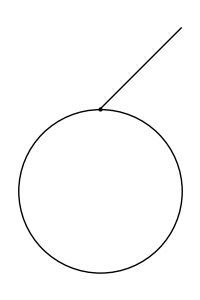

```mathematica
Graphics[{Point[{0,1}],Line[{{0,1},{1,2}}],Circle[]},ImageSize->200]
```

```mathematica
pts=RandomReal[{-10,10},{20,3}]
```

{{7.61873,-8.07332,-1.97083},{5.79011,-4.52453,7.94583},{-4.26624,-0.240249,3.63966},{-7.5327,3.03331,-6.18589},{6.63797,-1.14801,-9.22442},{0.233252,4.92036,8.43111},{7.92809,4.25644,-7.32967},{0.443786,-3.89411,-2.43506},{5.17132,6.38393,5.4724},{-6.07495,-8.01482,9.2614},{-2.44396,-1.29715,6.53187},{-0.192168,-3.23668,0.0881768},{-9.98203,-8.6155,-5.09155},{7.60384,4.78165,7.23034},{-4.34083,-1.41259,4.28313},{2.86345,-2.39736,7.63705},{-8.92977,5.65018,-5.50219},{-3.40247,-2.33304,1.01139},{4.64578,2.97231,-1.30975},{8.32098,-5.11568,4.7886}}

```mathematica
Graphics3D[{Red,PointSize@0.02,Point/@pts,Black,Line[pts]},Axes->True,Boxed->False,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Graphics3D[{White,PointSize@0.02,Cone[]},Axes->True,Boxed->False,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Graphics3D[{Lighting->None,Sphere[{0,0,0},1],Lighting->{{"Point",Red,{0,0,8}}},Sphere[{4,0,0},2],Lighting->{{"Point",White,{0,0,-4}}},Sphere[{10,0,0},3]}]
```

-Graphics3D-

```mathematica
pyrpts={{0,0,0},{0,1,0},{1,1,0},{1,0,0},{1/2,1/2,1}}
```

{{0,0,0},{0,1,0},{1,1,0},{1,0,0},{1/2,1/2,1}}

```mathematica
map={{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}}
```

{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}}

```mathematica
Graphics3D[{Opacity[0.1],GraphicsComplex[pyrpts,Polygon[map]]}]
```

-Graphics3D-

```mathematica
map1={{1,2,3,4,1},{1,5},{2,5},{3,5},{4,5}}
```

{{1,2,3,4,1},{1,5},{2,5},{3,5},{4,5}}

```mathematica
Graphics3D[{Opacity[0.8],GraphicsComplex[pyrpts,Line[map1]],Red,PointSize@0.03,Point/@pyrpts}]
```

-Graphics3D-

## Высокоуровневая графика

```mathematica
Plot3D[x^2-y^2,{x,-20,20},{y,-20,20},Mesh->Automatic]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/10},{t,0,20}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t]Cos[v],Sin[t]*Sin[v],Cos[t]},{t,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
Manipulate[Show[Graphics3D[{Point[{Sin[a],Cos[a],a/10}]},PlotRange->{{-5,5},{-5,5},{0,4}}],ParametricPlot3D[{t/10 Sin[t],t/10 Cos[t],t/10},{t,0,a},PlotStyle->Dashed]],{a,0.1,30}]
```

```mathematica
ParametricPlot3D[{2+t,3+2t,3t},{t,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[2x-3y+2,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
test=RegionIntersection[Cylinder[],Polygon[pyrpts//Most]]
```

BooleanRegion[#1&&#2&,{Cylinder[{{0,0,-1},{0,0,1}}],Polygon[…]}]

```mathematica
Region[test]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Opacity[0.2],Cylinder[],Polygon[pyrpts//Most]}],Region[test]]
```

-Graphics3D-

```mathematica
test=RegionIntersection[Cylinder[{{1,0,-4},{1,0,4}},1],Sphere[{0,0,0},2]]
```

BooleanRegion[#1&&#2&,{Cylinder[{{1,0,-4},{1,0,4}},1],Sphere[{0,0,0},2]}]

```mathematica
Show[Graphics3D[{Opacity[0.4],Cylinder[{{1,0,-4},{1,0,4}},1],Sphere[{0,0,0},2]}],Region[test],ParametricPlot3D[{1+Cos[t],Sin[t],2Sin[t/2]},{t,-2π,2π},PlotStyle->{Thick,Red}]]
```

-Graphics3D-

```mathematica
ClearAll@givePoint
```

```mathematica
givePoint[line:{vx_,vy_,vz_},plane_]:=plane/.MapThread[#1->#2&,{{x,y,z},line}]//Solve//line/.#&
```

```mathematica
givePoint[{t,t,t+1},x-y-z==0]
```

{{-1,-1,0}}

```mathematica
testline={t,t,t+1}
testplane=x-y-z==0
```

{t,t,1+t}

x-y-z==0

```mathematica
testplane/.MapThread[#1->#2&,{{x,y,z},testline}]//Solve//testline/.#&
```

{{-1,-1,0}}

```mathematica
x-y-z-1==0//Solve[#,z]&//Values//First//First
```

-1+x-y

```mathematica
Show[Plot3D[x-y-z==0//Solve[#,z]&//Values//First//First,{x,-10,10},{y,-10,10}],ParametricPlot3D[{t,t,t+1},{t,-10,10}],Graphics3D[{Red,PointSize@0.03,Point/@givePoint[{t,t,t+1},x-y-z==0]}]]
```

-Graphics3D-